```mathematica
(* After Quiz...*)
```

```mathematica
?Product
```

Product[f,{i,i_max}] evaluates the product ∏_(i=1)^i_max f. 
Product[f,{i,i_min,i_max}] starts with i=i_min. 
Product[f,{i,i_min,i_max,di}] uses steps di. 
Product[expr,{i,{i_1,i_2,…}}] uses successive values i_1,i_2,….
Product[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple product ∏_(i=i_min)^i_max ∏_(j=j_min)^j_max … f.

```mathematica
Product[Exp[i x],{i,1,10}]
```

ⅇ^(55 x)

```mathematica
Product[Exp[Sin[x]],{x,1,10}](* terms are Multiplying,and powers are added.*)
```

ⅇ^(Sin[1]+Sin[2]+Sin[3]+Sin[4]+Sin[5]+Sin[6]+Sin[7]+Sin[8]+Sin[9]+Sin[10])

```mathematica
?Sum
```

Sum[f,{i,i_max}] evaluates the sum ∑_(i=1)^i_max f. 
Sum[f,{i,i_min,i_max}] starts with i=i_min. 
Sum[f,{i,i_min,i_max,di}] uses steps di. 
Sum[expr,{i,{i_1,i_2,…}}] uses successive values i_1,i_2,….
Sum[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple sum ∑_(i=i_min)^i_max ∑_(j=j_min)^j_max …f.

```mathematica
(* Calculate the total potential energy(Use Sum command bcz of  Total energy.) of charges =k q1 q2/r *)
```

```mathematica
Sum[9 10^9 0.0003  n^2 (-1)^(n+1) 0.0003 m^2  (-1)^(m+1)/Abs[m/20-n/20],{n,1,19},{m,n+1,20}](*Discrete sum.bcz we have discretized values of distance.*)
```

-7.41201×10^9

```mathematica
(* TOPIC::: OPTIMIZATION:  *)
```

```mathematica
(* Continous Commands=  Countable Infinity: jiska start likh sakty hen. like =1,2,3,......
  Uncountable Infinity:Infinitesimel no,jiska start b ni bta sakty.*)
```

```mathematica
(* Max ,Min are the Discrete Commands.*)
?Min
(* to graph the output of Min we use ListPlot Command*)
```

Min[x_1,x_2,…] yields the numerically smallest of the x_i. 
Min[{x_1,x_2,…},{y_1,…},…] yields the smallest element of any of the lists.

```mathematica
?Max
```

Max[x_1,x_2,…] yields the numerically largest of the x_i. 
Max[{x_1,x_2,…},{y_1,…},…] yields the largest element of any of the lists.

```mathematica
(* Continous Commands=Minimize, FindMinimum *)
```

```mathematica
?Minimize(* Symbolic CommAND,,,,,,combination of  D+Solve *)
(* to graph the output of Minimize we use Plot(Numerical command) Command *)
```

Minimize[f,x] minimizes f with respect to x.
Minimize[f,{x,y,…}] minimizes f with respect to x, y, …. 
Minimize[{f,cons},{x,y,…}] minimizes f subject to the constraints cons. 
Minimize[{f,cons},{x,y,…},dom] minimizes with variables over the domain dom, typically Reals or Integers.

```mathematica
?FindMinimum(*combination of  D+FindRoot*)
```

RowBox[{"FindMinimum", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}]}], "]"}] searches for a local minimum in StyleBox["f", "TI"], starting from the point RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}]. 
RowBox[{"FindMinimum", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] searches for a local minimum in a function of several variables. 
RowBox[{"FindMinimum", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] searches for a local minimum subject to the constraints StyleBox["cons", "TI"].
RowBox[{"FindMinimum", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] starts from a point within the region defined by the constraints.

```mathematica
?FindRoot
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.

```mathematica
(* Lecture 14 *)
```

```mathematica
(* Question: Find numarically the work done by a spring in extension from 1-4cm with such a spring constant that, Magnitude of force F=5N at extension=3cm.*)
```

```mathematica
a=Solve[5==k 3 10^-2];b=k/.a[[1]];NIntegrate[-b x,{x,1 10^-2,4 10^-2}]
```

-0.125

```mathematica
(* Question:Find the smallest and largest of given values.*)
Min[2.3,Pi,1,-2/3,-0.01]//N
" Largest no "
Max[2.3,Pi,1,-2/3,-0.01]//N
```

-0.666667

Largest no

3.14159

```mathematica
(* Find the " Least " potential energy amongst those generated by  charge =k q1 q2/r *)
```

```mathematica
a=Table[9 10^9 0.0003  n^2 (-1)^(n+1) 0.0003 m^2  (-1)^(m+1)/Abs[m/20-n/20],{n,1,19},{m,n+1,20}];Min[a]
```

-2.33928×10^9

```mathematica
(* Lecture 15 *)
```

```mathematica
(* Find the Local min of given eq. near 1 and verify it satisfy the 1st and 2nd Derivative tests.*)
```

```mathematica
(*f=FindMinimum[3x^3-4x+Sin[x],{x,1}]
j=x/.f[[2]]*)
```

```mathematica
(*   {-1.1875668063698543,{x->0.5935821201095499}}  *)
```

```mathematica
Clear[a]
```

```mathematica
?Sign
```

Sign[x] gives -1, 0, or 1 depending on whether x is negative, zero, or positive.

```mathematica
a=3x^3-4x+Sin[x];b=x/.FindMinimum[a,{x,1}][[2]]
" First Derivative Test "
D[a,x]/.x->b
" Second Derivative Test "
Sign[D[a,{x,2}]/.x->b]
```

0.593582

First Derivative Test

```mathematica
4.0610181883948826*^-11(* numerical commands = FindMinimum,FindRoot,,,,,,thatswhy it does not return you exactly zero.*)
```

Second Derivative Test

1

```mathematica
(*Optional*)
```

```mathematica
a=3x^3-4x+Sin[x];b=x/.FindMinimum[3x^3-4x+Sin[x],{x,1}][[2]]
" First Derivative Test "
D[a,x]/.x->b
" Second Derivative Test "
If[Sign[D[a,{x,2}]/.x->b]==1,"Local Mini","Local max"]
```

0.593582

First Derivative Test

```mathematica
4.061029290625129*^-11
```

Second Derivative Test

Local Mini

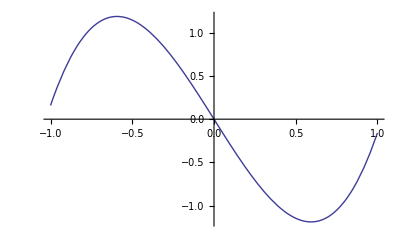

```mathematica
Plot[3x^3-4x+Sin[x],{x,-1,1},PlotRange->All]
```

```mathematica
(* Q: Find the equilibrium position(Numarical Value of independent variable) of q=2.1micro c,b/t Q1=Q2=4.1 micro c,Q1,Q2 are separated by 3cm.Display Energy.Using energy Considerations,make sure that 3 cm>x>0 .*)
```

```mathematica
(* we cant use FindMinimum Command bcz we dont have initial value.if we add a constant in 1st derivative, result remains same.*)
```

```mathematica
k=.
```

```mathematica
k=Minimize[ {9 10^9  (4.1 10^-6 2.1 10^-6/x+4.1 10^-6 2.1 10^-6/(3/100-x)),3/100>x>0},x]
" Equilibrium Position "
x/.k[[2]]
" Energy "
k[[1]]
```

```mathematica
{10.332,{x->0.015000000000000003}}(*just to see*)
```

Equilibrium Position

0.015

Energy

10.332